```mathematica
(*Calculate decomposition into binomial coefficients*)

BinomDecomp[n_,i_]:=Select[Module[
{a={},m, loc = n},
For[k=i, k≥1, k--,
m=k;
While[Binomial[m,k]<=loc, m+=1];
AppendTo[a,{m-1,k}];
loc-=Binomial[m-1,k]
];
a
],#[[2]]≠#[[1]]+1&]

(*Accepts a binomial decomp and shift, then prints new sum of binomials. r=0 gives original n*)
Kruskal[decomp_,r_]:=Total[Map[Binomial[#[[1]] , #[[2]]-r ] &, decomp]]

test= BinomDecomp[20,4]
Kruskal[test,0] (*Gives back 20 as expected*)
Kruskal[test,1]
```

{{6,4},{4,3},{2,2}}

20

28

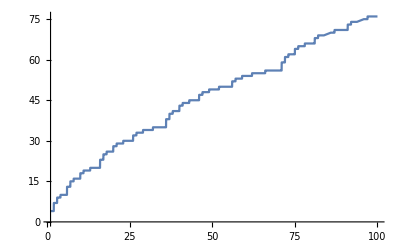

```mathematica
i=4;
r=1;
Plot[Kruskal[ BinomDecomp[n, i]  ,r], {n,1,100}]
```